# Data generation

## TODO

## Data format

Artificial data generation for clulstering varidity.

Data structire:
<Model and annotation>
;
<Dimension>[\tab]<Number of clusters>[\tab]<Number of samples>[\tab]<Number of background points>
;
<Cluster centers (model): matrix with tab delimiter>
;
<Samples: matrix with tab delimiter>
;

## Preparation

```mathematica
(*dir="/Users/amanokou/gitsrc/"*)
```

```mathematica
(*dir="/home/kamano/gitsrc/"*)
```

```mathematica
dir="/Users/kouamano/gitsrc/"
```

/Users/kouamano/gitsrc/

```mathematica
Get[dir<>"MATH_SCRIPT/SCRIPTS/polar.txt"]
```

```mathematica
SetDirectory[dir<>"ClusteringAdequation/generative-data"]
```

/Users/kouamano/gitsrc/ClusteringAdequation/generative-data

## Programs

```mathematica
strDataToExportStr[n_]:=StringJoin[Riffle[{anntS[n],dimS[n],centersS[n],samplesS[n]},";\n"]]
```

```mathematica
distanceMat[mat_]:=Module[
{n},
n=Length[mat];
Table[EuclideanDistance[mat[[i]],mat[[j]]],{i,n},{j,n}]
]
```

## 2D

### data 1 (general)

```mathematica
id=1
```

1

```mathematica
anntS[id]="Model: central random, circles, one radius, triangle.\n"
```

Model: central random, circles, one radius, triangle.

```mathematica
dim[id]=2;
numClass[id]=3;
numSample[id]={100,100,100};
numBG[id]={0};
```

```mathematica
dimS[id]=StringJoin[Riffle[{ToString[dim[id]],ToString[numClass[id]],ToString[numSample[id]],ToString[numBG[id]]},"\t"],"\n"]
```

2	3	{100, 100, 100}	{0}

```mathematica
centers[id]=Map[polarToxy[N[{1,#}]]&,Table[2Pi/numClass[id] n,{n,0,2}]]
```

{{1.,0.},{-0.5,0.866025},{-0.5,-0.866025}}

```mathematica
centersS[id]=ExportString[centers[id],"TSV"]<>"\n"
```

1.	0.
-0.4999999999999998	0.8660254037844387
-0.5000000000000004	-0.8660254037844384

```mathematica
distanceMat[centers[id]]
```

{{0.,1.73205,1.73205},{1.73205,0.,1.73205},{1.73205,1.73205,0.}}

```mathematica
distMean[id]=Tr[Flatten[distanceMat[centers[id]]]]/(numClass[id]^2-numClass[id])
```

1.73205

```mathematica
samples[id]=Table[Map[#+centers[id][[n]]&,Table[polarToxy[{RandomReal[{0,distMean[id]/2}],RandomReal[{0,2Pi}]}],{numSample[id][[n]]}]],{n,numClass[id]}];
```

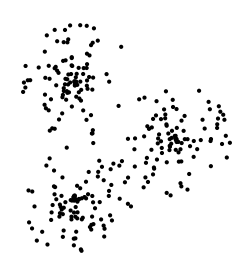

```mathematica
Graphics[Map[Point[#]&,samples[id],{2}]]
```

```mathematica
samplesS[id]=ExportString[Flatten[samples[id],1],"TSV"]<>"\n";
```

全サンプルの平均半径

```mathematica
totalCenter[id]=Mean[Flatten[samples[id],1]]
```

{-0.00908535,-0.0138822}

```mathematica
totalR[id]=Mean[Map[EuclideanDistance[totalCenter[id],#]&,Flatten[samples[id],1]]]
```

1.09822

各クラスタの平均半径

```mathematica
clCenters[id]=Map[Mean,samples[id]]
```

{{0.999658,0.001975},{-0.578679,0.907486},{-0.448235,-0.951108}}

```mathematica
clRs[id]=Table[Map[EuclideanDistance[clCenters[id][[i]],#]&,samples[id][[i]]]//Mean,{i,Length[clCenters[id]]}]
```

{0.43623,0.413608,0.417955}

Export 3f iles:

```mathematica
Export["data1.tsv",strDataToExportStr[id],"String"]
```

data1.tsv

```mathematica
Export["data1.ans.totalR",totalR[id],"Table"]
```

data1.ans.totalR

```mathematica
Export["data1.ans.clRs",clRs[id],"Table"]
```

data1.ans.clRs

### data 2 (unbalanced)

```mathematica
id=2
```

2

```mathematica
anntS[id]="Model: unbalanced central random, circles, radiuses.\n"
```

Model: unbalanced central random, circles, radiuses.

```mathematica
dim[id]=2;
numClass[id]=3;
numSample[id]={200,100,50};
numBG[id]={0};
```

```mathematica
dimS[id]=StringJoin[Riffle[{ToString[dim[id]],ToString[numClass[id]],ToString[numSample[id]],ToString[numBG[id]]},"\t"],"\n"]
```

2	3	{200, 100, 50}	{0}

```mathematica
centers[id]={{0,0},{0.5,-1},{-0.5,-0.75}}
```

{{0,0},{0.5,-1},{-0.5,-0.75}}

```mathematica
centersS[id]=ExportString[centers[id],"TSV"]<>"\n"
```

0	0
0.5	-1
-0.5	-0.75

```mathematica
distanceMat[centers[id]]
```

{{0,1.11803,0.901388},{1.11803,0.,1.03078},{0.901388,1.03078,0.}}

```mathematica
distMean[id]=Tr[Flatten[distanceMat[centers[id]]]]/(numClass[id]^2-numClass[id])
```

1.01673

```mathematica
radius[id]={distMean[id]*0.6,distMean[id]*0.4,distMean[id]*0.2}
```

{0.61004,0.406693,0.203347}

```mathematica
samples[id]=Table[Map[#+centers[id][[n]]&,Table[polarToxy[{RandomReal[{0,radius[id][[n]]}],RandomReal[{0,2Pi}]}],{numSample[id][[n]]}]],{n,numClass[id]}];
```

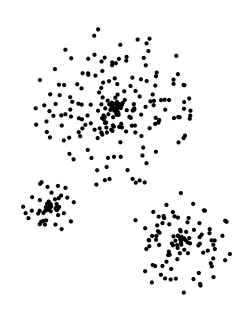

```mathematica
Graphics[Map[Point[#]&,samples[id],{2}]]
```

```mathematica
samplesS[id]=ExportString[Flatten[samples[id],1],"TSV"]<>"\n";
```

全サンプルの平均半径

```mathematica
id=2
```

2

```mathematica
totalCenter[id]=Mean[Flatten[samples[id],1]]
```

{0.0767934,-0.402737}

```mathematica
totalR[id]=Mean[Map[EuclideanDistance[totalCenter[id],#]&,Flatten[samples[id],1]]]
```

0.599281

各クラスタの平均半径

```mathematica
clCenters[id]=Map[Mean,samples[id]]
```

{{0.00661808,-0.0061394},{0.503128,-1.02132},{-0.495174,-0.751958}}

```mathematica
clRs[id]=Table[Map[EuclideanDistance[clCenters[id][[i]],#]&,samples[id][[i]]]//Mean,{i,Length[clCenters[id]]}]
```

{0.307774,0.194204,0.0967241}

```mathematica
Export["data2.tsv",strDataToExportStr[2],"String"]
```

data2.tsv

```mathematica
Export["data2.ans.totalR",totalR[id],"Table"]
```

data2.ans.totalR

```mathematica
Export["data2.ans.clRs",clRs[id],"Table"]
```

data2.ans.clRs

### data 4 (sub class)

```mathematica
anntS[4]="Model: central random , circles, one radius, subclusters.\n"
```

Model: central random , circles, one radius, subclusters.

```mathematica
dim[4]=2;
numClass[4]=4;
numSample[4]={100,100,100,100};
numBG[4]={0};
```

```mathematica
dimS[4]=StringJoin[Riffle[{ToString[dim[4]],ToString[numClass[4]],ToString[numSample[4]],ToString[numBG[4]]},"\t"],"\n"]
```

2	4	{100, 100, 100, 100}	{0}

```mathematica
centers[4]={{2,1},{2,-1},{-2,1},{-2,-1}}
```

{{2,1},{2,-1},{-2,1},{-2,-1}}

```mathematica
centersS[4]=ExportString[centers[4],"TSV"]<>"\n"
```

2	1
2	-1
-2	1
-2	-1

```mathematica
distMean[4]=Tr[Flatten[distanceMat[centers[4]]//N]]/(numClass[4]^2-numClass[4])
```

3.49071

```mathematica
samples[4,"class"]=Table[Map[#+centers[4][[n]]&,Table[polarToxy[{RandomReal[{0,distMean[4]/4}],RandomReal[{0,2Pi}]}],{numSample[4][[n]]}]],{n,numClass[4]}];
```

```mathematica
maxmin[4]=Map[{Max[#],Min[#]}&,Transpose[Flatten[samples[4,"class"],1]]]
```

{{2.82111,-2.83871},{1.80785,-1.80794}}

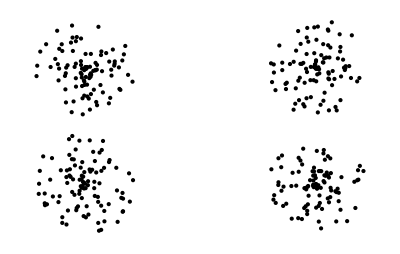

```mathematica
Graphics[Map[Point[#]&,Flatten[samples[4,"class"],1]]]
```

```mathematica
samplesS[4]=ExportString[Flatten[samples[4,"class"],1],"TSV"]<>"\n";
```

全サンプルの平均半径

```mathematica
id=4
```

4

```mathematica
totalCenter[id]=Mean[Flatten[samples[id,"class"],1]]
```

{-0.00107921,-0.0187529}

```mathematica
totalR[id]=Mean[Map[EuclideanDistance[totalCenter[id],#]&,Flatten[samples[id,"class"],1]]]
```

2.26037

各クラスタの平均半径

```mathematica
clCenters[id]=Map[Mean,samples[id,"class"]]
```

{{1.99976,0.999922},{1.98934,-1.02659},{-1.97808,0.966545},{-2.01533,-1.01489}}

```mathematica
clRs[id]=Table[Map[EuclideanDistance[clCenters[id][[i]],#]&,samples[id,"class"][[i]]]//Mean,{i,Length[clCenters[id]]}]
```

{0.443725,0.408025,0.411388,0.474811}

```mathematica
Export["data4.tsv",strDataToExportStr[4],"String"]
```

data4.tsv

```mathematica
Export["data4.ans.totalR",totalR[id],"Table"]
```

data4.ans.totalR

```mathematica
Export["data4.ans.clRs",clRs[id],"Table"]
```

data4.ans.clRs

### data 5 (ring + disc)

```mathematica
anntS[5]="Model: central random , disc + ring.\n"
```

Model: central random , disc + ring.

```mathematica
dim[5]=2;
numClass[5]=2;
numSample[5]={100,200};
numBG[5]={0};
```

```mathematica
dimS[5]=StringJoin[Riffle[{ToString[dim[5]],ToString[numClass[5]],ToString[numSample[5]],ToString[numBG[5]]},"\t"],"\n"]
```

2	2	{100, 200}	{0}

```mathematica
centers[5]={{0,0},{0,0}}
```

{{0,0},{0,0}}

```mathematica
centersS[5]=ExportString[centers[5],"TSV"]<>"\n"
```

0	0
0	0

```mathematica
samples[5,"disc"]=Map[polarToxy[#]&,Table[{RandomReal[{0,1}],RandomReal[{0,2 Pi}]},{numSample[5][[1]]}]];
```

```mathematica
samples[5,"ring"]=Map[polarToxy[#]&,Table[{RandomReal[{1.5,2}],RandomReal[{0,2 Pi}]},{numSample[5][[2]]}]];
```

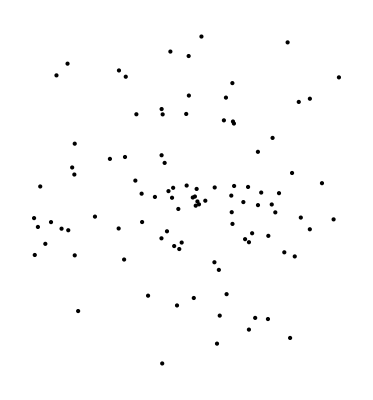

```mathematica
Graphics[Map[Point[#]&,samples[5,"disc"]]]
```

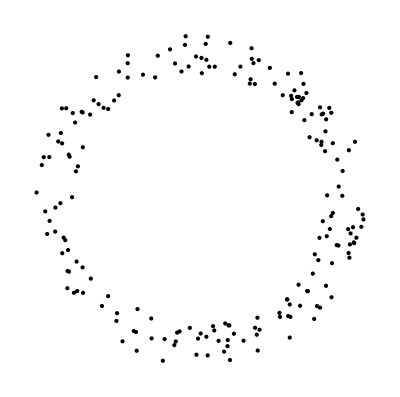

```mathematica
Graphics[Map[Point[#]&,samples[5,"ring"]]]
```

```mathematica
samples[5,"class"]=List[samples[5,"disc"],samples[5,"ring"]];
```

```mathematica
(*samplesS[1]=ExportString[Flatten[samples[1],1],"TSV"]<>"\n";*)
```

```mathematica
samplesS[5]=ExportString[Flatten[samples[5,"class"],1],"TSV"]<>"\n";
```

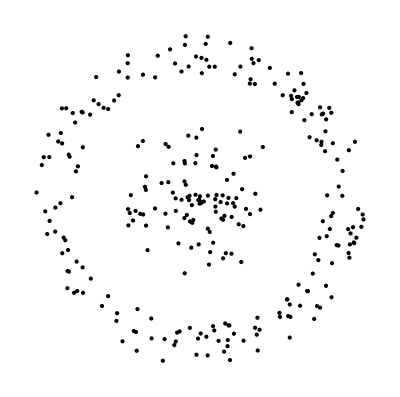

```mathematica
Map[Point[#]&,samples[5,"class"]]//Graphics
```

全サンプルの平均半径

```mathematica
id=5
```

5

```mathematica
totalCenter[id]=Mean[Flatten[samples[id,"class"],1]]
```

{0.131717,0.00724475}

```mathematica
totalR[id]=Mean[Map[EuclideanDistance[totalCenter[id],#]&,Flatten[samples[id,"class"],1]]]
```

1.32105

各クラスタの平均半径

```mathematica
clCenters[id]=Map[Mean,samples[id,"class"]]
```

{{-0.0253859,-0.00160386},{0.210268,0.0116691}}

```mathematica
clRs[id]=Table[Map[EuclideanDistance[clCenters[id][[i]],#]&,samples[id,"class"][[i]]]//Mean,{i,Length[clCenters[id]]}]
```

{0.494513,1.72042}

```mathematica
Export["data5.tsv",strDataToExportStr[5],"String"]
```

data5.tsv

```mathematica
Export["data5.ans.totalR",totalR[id],"Table"]
```

data5.ans.totalR

```mathematica
Export["data5.ans.clRs",clRs[id],"Table"]
```

data5.ans.clRs

### data 6 (spiral)

```mathematica
anntS[6]="Model: spiral x 3.\n"
```

Model: spiral x 3.

```mathematica
dim[6]=2;
numClass[6]=3;
numSample[6]={100,100,100};
numBG[6]={0};
```

```mathematica
dimS[6]=StringJoin[Riffle[{ToString[dim[6]],ToString[numClass[6]],ToString[numSample[6]],ToString[numBG[6]]},"\t"],"\n"]
```

2	3	{100, 100, 100}	{0}

```mathematica
origins[6]={{0,0},{0,0},{0,0}}
```

{{0,0},{0,0},{0,0}}

```mathematica
(samples[6,0]=Map[polarToxy[#]&,Table[{r,3r},{r,0.5,3-0.02,0.025}]])//Length
```

100

```mathematica
center[6,0]=Mean[samples[6,0]]
```

{0.0684864,0.339278}

```mathematica
(samples[6,1]=Map[polarToxy[#]&,Table[{r,3r+(2Pi/3)},{r,0.5,3-0.02,0.025}]])//Length
```

100

```mathematica
center[6,1]=Mean[samples[6,1]]
```

{-0.328066,-0.110328}

```mathematica
(samples[6,2]=Map[polarToxy[#]&,Table[{r,3r+(4Pi/3)},{r,0.5,3-0.02,0.025}]])//Length
```

100

```mathematica
center[6,2]=Mean[samples[6,2]]
```

{0.25958,-0.22895}

```mathematica
centers[6]={center[6,0],center[6,1],center[6,2]}
```

{{0.0684864,0.339278},{-0.328066,-0.110328},{0.25958,-0.22895}}

```mathematica
centersS[6]=ExportString[centers[6],"TSV"]<>"\n"
```

0.06848640517315346	0.3392778825308757
-0.3280664678005077	-0.11032797457161272
0.25958006262735384	-0.22894990795926298

```mathematica
samples[6,"class"]=List[samples[6,0],samples[6,1],samples[6,2]];
```

```mathematica
samplesS[6]=ExportString[Flatten[samples[6,"class"],1],"TSV"]<>"\n";
```

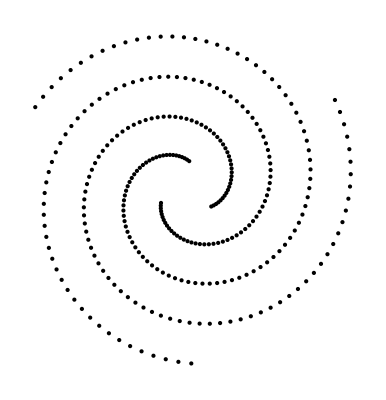

```mathematica
Map[Point[#]&,samples[6,"class"]]//Graphics
```

全サンプルの平均半径

```mathematica
id=6
```

6

```mathematica
totalCenter[id]=Mean[Flatten[samples[id,"class"],1]]
```

{-1.12503×10^-16,4.81097×10^-17}

```mathematica
totalR[id]=Mean[Map[EuclideanDistance[totalCenter[id],#]&,Flatten[samples[id,"class"],1]]]
```

1.7375

各クラスタの平均半径

```mathematica
clCenters[id]=Map[Mean,samples[id,"class"]]
```

{{0.0684864,0.339278},{-0.328066,-0.110328},{0.25958,-0.22895}}

```mathematica
clRs[id]=Table[Map[EuclideanDistance[clCenters[id][[i]],#]&,samples[id,"class"][[i]]]//Mean,{i,Length[clCenters[id]]}]
```

{1.71971,1.71971,1.71971}

```mathematica
Export["data6.tsv",strDataToExportStr[6],"String"]
```

data6.tsv

```mathematica
Export["data6.ans.totalR",totalR[id],"Table"]
```

data6.ans.totalR

```mathematica
Export["data6.ans.clRs",clRs[id],"Table"]
```

data6.ans.clRs

## Noisy

### data 3 (noisy)

```mathematica
anntS[3]="Model: central random + noise, circles, one radius, triangle.\n"
```

Model: central random + noise, circles, one radius, triangle.

```mathematica
dim[3]=2;
numClass[3]=3;
numSample[3]={100,100,100};
numBG[3]={150};
```

```mathematica
dimS[3]=StringJoin[Riffle[{ToString[dim[3]],ToString[numClass[3]],ToString[numSample[3]],ToString[numBG[3]]},"\t"],"\n"]
```

2	3	{100, 100, 100}	{150}

```mathematica
centers[3]=Map[polarToxy[N[{1,#}]]&,Table[2Pi/numClass[3] n,{n,0,2}]]
```

{{1.,0.},{-0.5,0.866025},{-0.5,-0.866025}}

```mathematica
centersS[3]=ExportString[centers[3],"TSV"]<>"\n"
```

1.	0.
-0.4999999999999998	0.8660254037844387
-0.5000000000000004	-0.8660254037844384

```mathematica
distanceMat[centers[3]]
```

{{0.,1.73205,1.73205},{1.73205,0.,1.73205},{1.73205,1.73205,0.}}

```mathematica
distMean[3]=Tr[Flatten[distanceMat[centers[3]]]]/(numClass[3]^2-numClass[3])
```

1.73205

```mathematica
samples[3,"class"]=Table[Map[#+centers[3][[n]]&,Table[polarToxy[{RandomReal[{0,distMean[3]/3}],RandomReal[{0,2Pi}]}],{numSample[3][[n]]}]],{n,numClass[3]}];
```

```mathematica
maxmin[3]=Map[{Max[#],Min[#]}&,Transpose[Flatten[samples[3,"class"],1]]]
```

{{1.55869,-1.06865},{1.42955,-1.41784}}

```mathematica
samples[3,"background"]=Table[{RandomReal[maxmin[3][[1]]],RandomReal[maxmin[3][[2]]]},{numBG[3][[1]]}];
```

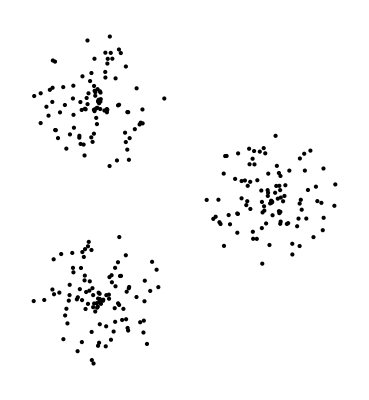

```mathematica
Graphics[Map[Point[#]&,Flatten[samples[3,"class"],1]]]
```

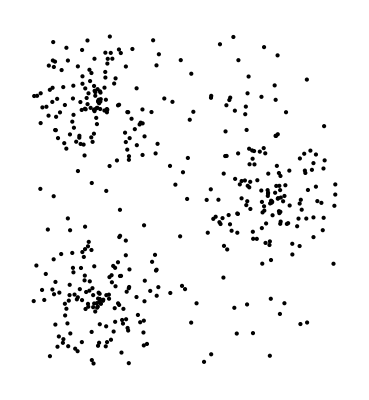

```mathematica
Graphics[Map[Point[#]&,Join[Flatten[samples[3,"class"],1],samples[3,"background"]]]]
```

```mathematica
samplesS[3]=ExportString[Join[Flatten[samples[3,"class"],1],samples[3,"background"]],"TSV"]<>"\n";
```

```mathematica
(*(samples[3,"All"]=Append[samples[3,"class"],samples[3,"background"]])//Length*)
```

全サンプルの平均半径

```mathematica
id=3
```

3

```mathematica
totalCenter[id]=Mean[Flatten[samples[id,"class"],1]]
```

{-0.0142825,0.00539208}

```mathematica
totalR[id]=Mean[Map[EuclideanDistance[totalCenter[id],#]&,Flatten[samples[id,"class"],1]]]
```

1.01568

各クラスタの平均半径

```mathematica
clCenters[id]=Map[Mean,samples[id,"class"]]
```

{{0.9875,0.0198738},{-0.538636,0.840139},{-0.491712,-0.843836}}

```mathematica
clRs[id]=Table[Map[EuclideanDistance[clCenters[id][[i]],#]&,samples[id,"class"][[i]]]//Mean,{i,Length[clCenters[id]]}]
```

{0.30804,0.283227,0.285389}

```mathematica
Export["data3.tsv",strDataToExportStr[3],"String"]
```

data3.tsv

```mathematica
Export["data3.ans.totalR",totalR[id],"Table"]
```

data3.ans.totalR

```mathematica
Export["data3.ans.clRs",clRs[id],"Table"]
```

data3.ans.clRs

## 3D

### data 7 (chain)

```mathematica
anntS[7]="Model: double chain.\n"
```

Model: double chain.

```mathematica
dim[7]=3;
numClass[7]=2;
numSample[7]={150,150};
numBG[7]={0};
```

```mathematica
dimS[7]=StringJoin[Riffle[{ToString[dim[7]],ToString[numClass[7]],ToString[numSample[7]],ToString[numBG[7]]},"\t"],"\n"]
```

3	2	{150, 150}	{0}

```mathematica
centers[7]={{0,0,0},{1,0,0}}
```

{{0,0,0},{1,0,0}}

```mathematica
(*origins[6]={{0,0},{0,0},{0,0}}*)
```

```mathematica
centersS[7]=ExportString[centers[7],"TSV"]<>"\n"
```

0	0	0
1	0	0

```mathematica
samples[7,1]=Map[sPolarToxyz[#]&,Table[{1,Pi/2,ph},{ph,0,2Pi-2Pi/150,2Pi/150}]];
```

```mathematica
Map[Point[#]&,samples[7,1]]//Length
```

150

```mathematica
Map[Point[#]&,samples[7,1]]//Graphics3D
```

-Graphics3D-

```mathematica
samples[7,2]=Map[sPolarToxyz[#]&,Table[{1,th,0},{th,0,2Pi-2Pi/150,2Pi/150}]];
```

```mathematica
Map[Point[#]&,samples[7,2]]//Length
```

150

```mathematica
Map[Point[#]&,samples[7,2]]//Graphics3D
```

-Graphics3D-

```mathematica
(*(samples[7,"All"]=Join[samples[7,1],Map[#+centers[7][[2]]&,samples[7,2]]]//N)//Length*)
```

```mathematica
(samples[7,"class"]=List[samples[7,1],Map[#+centers[7][[2]]&,samples[7,2]]]//N)//Length
```

2

```mathematica
Map[Point[#]&,samples[7,"class"]]//Graphics3D
```

-Graphics3D-

```mathematica
samplesS[7]=ExportString[Flatten[samples[7,"class"],1],"TSV"]<>"\n";
```

全サンプルの平均半径

```mathematica
id=7
```

7

```mathematica
totalCenter[id]=Mean[Flatten[samples[id,"class"],1]]
```

{0.5,-2.7293×10^-18,2.96059×10^-18}

```mathematica
totalR[id]=Mean[Map[EuclideanDistance[totalCenter[id],#]&,Flatten[samples[id,"class"],1]]]
```

1.06354

各クラスタの平均半径

```mathematica
clCenters[id]=Map[Mean,samples[id,"class"]]
```

{{5.92119×10^-18,-5.4586×10^-18,0.},{1.,0.,5.92119×10^-18}}

```mathematica
clRs[id]=Table[Map[EuclideanDistance[clCenters[id][[i]],#]&,samples[id,"class"][[i]]]//Mean,{i,Length[clCenters[id]]}]
```

{1.,1.}

```mathematica
Export["data7.tsv",strDataToExportStr[7],"String"]
```

data7.tsv

```mathematica
Export["data7.ans.totalR",totalR[id],"Table"]
```

data7.ans.totalR

```mathematica
Export["data7.ans.clRs",clRs[id],"Table"]
```

data7.ans.clRs

## Many class

### data 8 (4 classes)

```mathematica
anntS[8]="Model: central random , circles, one radius, 2d-4class.\n"
```

Model: central random , circles, one radius, 2d-4class.

```mathematica
dim[8]=2;
numClass[8]=4;
numSample[8]={100,100,100,100};
numBG[8]={0};
```

```mathematica
dimS[8]=StringJoin[Riffle[{ToString[dim[8]],ToString[numClass[8]],ToString[numSample[8]],ToString[numBG[8]]},"\t"],"\n"]
```

2	4	{100, 100, 100, 100}	{0}

```mathematica
centers[8]={{2,2},{2,-2},{-2,2},{-2,-2}}
```

{{2,2},{2,-2},{-2,2},{-2,-2}}

```mathematica
centersS[8]=ExportString[centers[8],"TSV"]<>"\n"
```

2	2
2	-2
-2	2
-2	-2

```mathematica
distMean[8]=Tr[Flatten[distanceMat[centers[8]]//N]]/(numClass[8]^2-numClass[8])
```

4.55228

```mathematica
samples[8,"class"]=Table[Map[#+centers[8][[n]]&,Table[polarToxy[{RandomReal[{0,distMean[8]/4}],RandomReal[{0,2Pi}]}],{numSample[8][[n]]}]],{n,numClass[8]}];
```

```mathematica
maxmin[8]=Map[{Max[#],Min[#]}&,Transpose[Flatten[samples[8,"class"],1]]]
```

{{3.02416,-3.08307},{3.03559,-3.09913}}

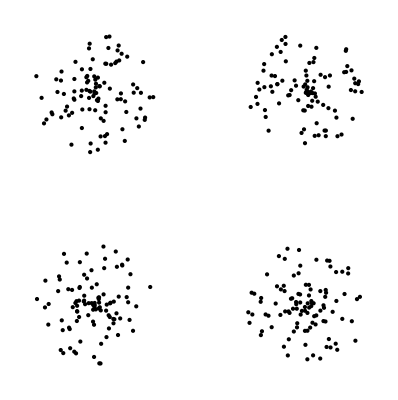

```mathematica
Graphics[Map[Point[#]&,Flatten[samples[8,"class"],1]]]
```

```mathematica
samplesS[8]=ExportString[Flatten[samples[8,"class"],1],"TSV"]<>"\n";
```

全サンプルの平均半径

```mathematica
id=8
```

8

```mathematica
totalCenter[id]=Mean[Flatten[samples[id,"class"],1]]
```

{-0.00499007,-0.00375513}

```mathematica
totalR[id]=Mean[Map[EuclideanDistance[totalCenter[id],#]&,Flatten[samples[id,"class"],1]]]
```

2.85603

各クラスタの平均半径

```mathematica
clCenters[id]=Map[Mean,samples[id,"class"]]
```

{{1.997,2.03279},{1.95175,-2.02187},{-1.9399,1.96113},{-2.02881,-1.98707}}

```mathematica
clRs[id]=Table[Map[EuclideanDistance[clCenters[id][[i]],#]&,samples[id,"class"][[i]]]//Mean,{i,Length[clCenters[id]]}]
```

{0.581389,0.596375,0.612352,0.55369}

```mathematica
Export["data8.tsv",strDataToExportStr[8],"String"]
```

data8.tsv

```mathematica
Export["data8.ans.totalR",totalR[id],"Table"]
```

data8.ans.totalR

```mathematica
Export["data8.ans.clRs",clRs[id],"Table"]
```

data8.ans.clRs

### data 9 (8 classes)

```mathematica
anntS[9]="Model: central random , circles, one radius, 2d-8class.\n"
```

Model: central random , circles, one radius, 2d-8class.

```mathematica
dim[9]=2;
numClass[9]=8;
numSample[9]={100,100,100,100,100,100,100,100};
numBG[9]={0};
```

```mathematica
dimS[9]=StringJoin[Riffle[{ToString[dim[9]],ToString[numClass[9]],ToString[numSample[9]],ToString[numBG[9]]},"\t"],"\n"]
```

2	8	{100, 100, 100, 100, 100, 100, 100, 100}	{0}

```mathematica
centers[9]={{7,7},{7,-7},{-7,7},{-7,-7},{0,20},{20,0},{0,-20},{-20,0}}
```

{{7,7},{7,-7},{-7,7},{-7,-7},{0,20},{20,0},{0,-20},{-20,0}}

```mathematica
centersS[9]=ExportString[centers[9],"TSV"]<>"\n"
```

7	7
7	-7
-7	7
-7	-7
0	20
20	0
0	-20
-20	0

```mathematica
distMean[9]=Tr[Flatten[distanceMat[centers[9]]//N]]/(numClass[9]^2-numClass[9])
```

22.4998

```mathematica
samples[9,"class"]=Table[Map[#+centers[9][[n]]&,Table[polarToxy[{RandomReal[{0,distMean[9]/4}],RandomReal[{0,2Pi}]}],{numSample[9][[n]]}]],{n,numClass[9]}];
```

```mathematica
maxmin[9]=Map[{Max[#],Min[#]}&,Transpose[Flatten[samples[9,"class"],1]]]
```

{{24.9382,-25.2337},{24.9529,-25.1708}}

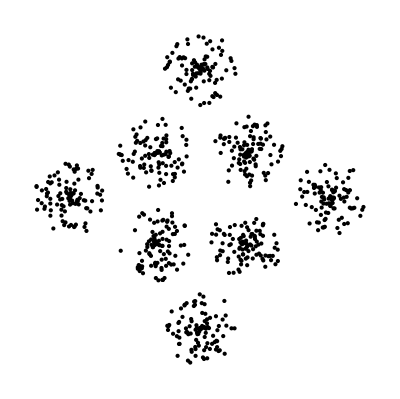

```mathematica
Graphics[Map[Point[#]&,Flatten[samples[9,"class"],1]]]
```

```mathematica
samplesS[9]=ExportString[Flatten[samples[9,"class"],1],"TSV"]<>"\n";
```

全サンプルの平均半径

```mathematica
id=9
```

9

```mathematica
totalCenter[id]=Mean[Flatten[samples[id,"class"],1]]
```

{-0.0489452,-0.0634667}

```mathematica
totalR[id]=Mean[Map[EuclideanDistance[totalCenter[id],#]&,Flatten[samples[id,"class"],1]]]
```

15.2185

各クラスタの平均半径

```mathematica
clCenters[id]=Map[Mean,samples[id,"class"]]
```

{{7.39242,7.31937},{6.89871,-7.16612},{-7.06112,6.78006},{-6.52072,-7.38446},{-0.313503,19.9041},{19.7713,-0.0639229},{-0.29044,-20.2257},{-20.2682,0.32889}}

```mathematica
clRs[id]=Table[Map[EuclideanDistance[clCenters[id][[i]],#]&,samples[id,"class"][[i]]]//Mean,{i,Length[clCenters[id]]}]
```

{2.8335,2.79809,2.96342,2.94436,2.85377,2.76174,2.94459,3.10532}

```mathematica
Export["data9.tsv",strDataToExportStr[9],"String"]
```

data9.tsv

```mathematica
Export["data9.ans.totalR",totalR[id],"Table"]
```

data9.ans.totalR

```mathematica
Export["data9.ans.clRs",clRs[id],"Table"]
```

data9.ans.clRs

### data 10 (3d-8 classes) (scale: base)

```mathematica
anntS[10]="Model: central random , circles, one radius, 3d-8class (base).\n"
```

Model: central random , circles, one radius, 3d-8class (base).

```mathematica
dim[10]=3;
numClass[10]=8;
numSample[10]={100,100,100,100,100,100,100,100};
numBG[10]={0};
```

```mathematica
dimS[10]=StringJoin[Riffle[{ToString[dim[10]],ToString[numClass[10]],ToString[numSample[10]],ToString[numBG[10]]},"\t"],"\n"]
```

3	8	{100, 100, 100, 100, 100, 100, 100, 100}	{0}

```mathematica
centers[10]=Tuples[{0,10},3]
```

{{0,0,0},{0,0,10},{0,10,0},{0,10,10},{10,0,0},{10,0,10},{10,10,0},{10,10,10}}

```mathematica
centersS[10]=ExportString[centers[10],"TSV"]<>"\n"
```

0	0	0
0	0	10
0	10	0
0	10	10
10	0	0
10	0	10
10	10	0
10	10	10

```mathematica
distMean[10]=Tr[Flatten[distanceMat[centers[10]]//N]]/(numClass[10]^2-numClass[10])
```

12.821

```mathematica
centers[10]
```

{{0,0,0},{0,0,10},{0,10,0},{0,10,10},{10,0,0},{10,0,10},{10,10,0},{10,10,10}}

```mathematica
samples[10,"class"]=Table[centers[10][[c]]+Table[RandomVariate[NormalDistribution[0,distMean[10]/16]],{3}],{c,numClass[10]},{100}];
```

```mathematica
maxmin[10]=Map[{Max[#],Min[#]}&,Transpose[Flatten[samples[10,"class"],1]]]
```

{{12.2968,-2.43748},{12.3392,-2.51772},{12.7624,-2.66109}}

```mathematica
Graphics3D[Map[Point[#]&,Flatten[samples[10,"class"],1]]]
```

-Graphics3D-

```mathematica
samplesS[10]=ExportString[Flatten[samples[10,"class"],1],"TSV"]<>"\n";
```

全サンプルの平均半径

```mathematica
id=10
```

10

```mathematica
totalCenter[id]=Mean[Flatten[samples[id,"class"],1]]
```

{5.02096,5.0356,4.95881}

```mathematica
totalR[id]=Mean[Map[EuclideanDistance[totalCenter[id],#]&,Flatten[samples[id,"class"],1]]]
```

8.76083

各クラスタの平均半径

```mathematica
clCenters[id]=Map[Mean,samples[id,"class"]]
```

{{0.00448883,-0.121635,-0.0592247},{-0.00141865,0.0128694,9.87471},{0.00850364,9.98699,-0.106676},{0.0221111,10.0779,10.0282},{10.0499,0.0972347,0.0639695},{10.069,0.116037,10.0425},{9.97023,10.0888,-0.127833},{10.0448,10.0266,9.95487}}

```mathematica
clRs[id]=Table[Map[EuclideanDistance[clCenters[id][[i]],#]&,samples[id,"class"][[i]]]//Mean,{i,Length[clCenters[id]]}]
```

{1.3766,1.28357,1.29755,1.2965,1.35093,1.36978,1.30901,1.21598}

```mathematica
Export["data10.tsv",strDataToExportStr[10],"String"]
```

data10.tsv

```mathematica
Export["data10.ans.totalR",totalR[id],"Table"]
```

data10.ans.totalR

```mathematica
Export["data10.ans.clRs",clRs[id],"Table"]
```

data10.ans.clRs

### data 10.2 (3d-8 classes) (scale: 2)

```mathematica
anntS[10.2]="Model: central random , circles, one radius, 3d-8class, scaled.\n"
```

Model: central random , circles, one radius, 3d-8class, scaled.

```mathematica
dim[10.2]=3;
numClass[10.2]=8;
numSample[10.2]={100,100,100,100,100,100,100,100};
numBG[10.2]={0};
```

```mathematica
dimS[10.2]=StringJoin[Riffle[{ToString[dim[10.2]],ToString[numClass[10.2]],ToString[numSample[10.2]],ToString[numBG[10.2]]},"\t"],"\n"]
```

3	8	{100, 100, 100, 100, 100, 100, 100, 100}	{0}

```mathematica
centers[10.2]=Tuples[{0,10},3]/4//N
```

{{0.,0.,0.},{0.,0.,2.5},{0.,2.5,0.},{0.,2.5,2.5},{2.5,0.,0.},{2.5,0.,2.5},{2.5,2.5,0.},{2.5,2.5,2.5}}

```mathematica
centersS[10.2]=ExportString[centers[10.2],"TSV"]<>"\n";
```

```mathematica
distMean[10.2]=Tr[Flatten[distanceMat[centers[10.2]]//N]]/(numClass[10.2]^2-numClass[10.2])
```

3.20525

```mathematica
samples[10.2,"class"]=Table[centers[10.2][[c]]+Table[RandomVariate[NormalDistribution[0,distMean[10.2]/10]],{3}],{c,numClass[10.2]},{100}];
```

```mathematica
maxmin[10.2]=Map[{Max[#],Min[#]}&,Transpose[Flatten[samples[10.2,"class"],1]]]
```

{{3.3031,-0.901448},{3.35205,-0.971053},{3.45304,-0.964572}}

```mathematica
Graphics3D[Map[Point[#]&,Flatten[samples[10.2,"class"],1]]]
```

-Graphics3D-

```mathematica
samplesS[10.2]=ExportString[Flatten[samples[10.2,"class"],1],"TSV"]<>"\n";
```

全サンプルの平均半径

```mathematica
id=10.2
```

10.2

```mathematica
totalCenter[id]=Mean[Flatten[samples[id,"class"],1]]
```

{1.25964,1.26372,1.24692}

```mathematica
totalR[id]=Mean[Map[EuclideanDistance[totalCenter[id],#]&,Flatten[samples[id,"class"],1]]]
```

2.21414

各クラスタの平均半径

```mathematica
clCenters[id]=Map[Mean,samples[id,"class"]]
```

{{0.0473878,0.019167,0.0068605},{0.0111656,0.0107819,2.49349},{0.0122624,2.53108,0.000700539},{-0.0115718,2.53519,2.52766},{2.50649,0.0156218,-0.00234732},{2.52876,-0.00507754,2.44453},{2.50635,2.52201,-0.0319871},{2.4763,2.48101,2.53647}}

```mathematica
clRs[id]=Table[Map[EuclideanDistance[clCenters[id][[i]],#]&,samples[id,"class"][[i]]]//Mean,{i,Length[clCenters[id]]}]
```

{0.499968,0.493508,0.505304,0.518383,0.510881,0.502191,0.514999,0.526312}

```mathematica
Export["data10-2.tsv",strDataToExportStr[10.2],"String"]
```

data10-2.tsv

```mathematica
Export["data10-2.ans.totalR",totalR[id],"Table"]
```

data10-2.ans.totalR

```mathematica
Export["data10-2.ans.clRs",clRs[id],"Table"]
```

data10-2.ans.clRs

### data 10.3 (3d-8 classes) (scale: 3)

```mathematica
anntS[10.3]="Model: central random , circles, one radius, 3d-8class, scaled(3).\n"
```

Model: central random , circles, one radius, 3d-8class, scaled(3).

```mathematica
dim[10.3]=3;
numClass[10.3]=8;
numSample[10.3]={100,100,100,100,100,100,100,100};
numBG[10.3]={0};
```

```mathematica
dimS[10.3]=StringJoin[Riffle[{ToString[dim[10.3]],ToString[numClass[10.3]],ToString[numSample[10.3]],ToString[numBG[10.3]]},"\t"],"\n"]
```

3	8	{100, 100, 100, 100, 100, 100, 100, 100}	{0}

```mathematica
centers[10.3]=Tuples[{0,10},3]/8//N
```

{{0.,0.,0.},{0.,0.,1.25},{0.,1.25,0.},{0.,1.25,1.25},{1.25,0.,0.},{1.25,0.,1.25},{1.25,1.25,0.},{1.25,1.25,1.25}}

```mathematica
centersS[10.3]=ExportString[centers[10.3],"TSV"]<>"\n"
```

0.	0.	0.
0.	0.	1.25
0.	1.25	0.
0.	1.25	1.25
1.25	0.	0.
1.25	0.	1.25
1.25	1.25	0.
1.25	1.25	1.25

```mathematica
distMean[10.3]=Tr[Flatten[distanceMat[centers[10.3]]//N]]/(numClass[10.3]^2-numClass[10.3])
```

1.60262

```mathematica
samples[10.3,"class"]=Table[centers[10.3][[c]]+Table[RandomVariate[NormalDistribution[0,distMean[10.3]/10]],{3}],{c,numClass[10.3]},{100}];
```

```mathematica
maxmin[10.3]=Map[{Max[#],Min[#]}&,Transpose[Flatten[samples[10.3,"class"],1]]]
```

{{1.65164,-0.373529},{1.66708,-0.457859},{1.70792,-0.446213}}

```mathematica
Graphics3D[Map[Point[#]&,Flatten[samples[10.3,"class"],1]]]
```

-Graphics3D-

```mathematica
samplesS[10.3]=ExportString[Flatten[samples[10.3,"class"],1],"TSV"]<>"\n";
```

全サンプルの平均半径

```mathematica
id=10.3
```

10.3

```mathematica
totalCenter[id]=Mean[Flatten[samples[id,"class"],1]]
```

{0.624094,0.623733,0.632594}

```mathematica
totalR[id]=Mean[Map[EuclideanDistance[totalCenter[id],#]&,Flatten[samples[id,"class"],1]]]
```

1.10226

各クラスタの平均半径

```mathematica
clCenters[id]=Map[Mean,samples[id,"class"]]
```

{{0.00619437,0.00501938,0.00624213},{0.00524592,-0.00286657,1.23104},{-0.0220432,1.23287,0.00270979},{0.0208043,1.26441,1.24232},{1.26094,-0.00220986,0.0157727},{1.25618,0.0253719,1.2871},{1.25629,1.24201,-0.0076422},{1.20915,1.22526,1.28321}}

```mathematica
clRs[id]=Table[Map[EuclideanDistance[clCenters[id][[i]],#]&,samples[id,"class"][[i]]]//Mean,{i,Length[clCenters[id]]}]
```

{0.247633,0.261781,0.247948,0.244893,0.249014,0.260949,0.238927,0.27275}

```mathematica
Export["data10-3.tsv",strDataToExportStr[10.3],"String"]
```

data10-3.tsv

```mathematica
Export["data10-3.ans.totalR",totalR[id],"Table"]
```

data10-3.ans.totalR

```mathematica
Export["data10-3.ans.clRs",clRs[id],"Table"]
```

data10-3.ans.clRs

### data 10.4 (3d-8 classes) (scale: 4)

```mathematica
id=10.4
```

10.4

```mathematica
anntS[id]="Model: central random , circles, one radius, 3d-8class, scaled(4).\n"
```

Model: central random , circles, one radius, 3d-8class, scaled(4).

```mathematica
dim[id]=3;
numClass[id]=8;
numSample[id]={100,100,100,100,100,100,100,100};
numBG[id]={0};
```

```mathematica
dimS[id]=StringJoin[Riffle[{ToString[dim[id]],ToString[numClass[id]],ToString[numSample[id]],ToString[numBG[id]]},"\t"],"\n"]
```

3	8	{100, 100, 100, 100, 100, 100, 100, 100}	{0}

```mathematica
centers[id]=Tuples[{0,10},3]/8//N
```

{{0.,0.,0.},{0.,0.,1.25},{0.,1.25,0.},{0.,1.25,1.25},{1.25,0.,0.},{1.25,0.,1.25},{1.25,1.25,0.},{1.25,1.25,1.25}}

```mathematica
centersS[id]=ExportString[centers[id],"TSV"]<>"\n"
```

0.	0.	0.
0.	0.	1.25
0.	1.25	0.
0.	1.25	1.25
1.25	0.	0.
1.25	0.	1.25
1.25	1.25	0.
1.25	1.25	1.25

```mathematica
distMean[id]=Tr[Flatten[distanceMat[centers[id]]//N]]/(numClass[id]^2-numClass[id])
```

1.60262

```mathematica
samples[id,"class"]=Table[centers[id][[c]]+Table[RandomVariate[NormalDistribution[0,distMean[id]/15]],{3}],{c,numClass[id]},{100}];
```

```mathematica
maxmin[id]=Map[{Max[#],Min[#]}&,Transpose[Flatten[samples[id,"class"],1]]]
```

{{1.51161,-0.335611},{1.52794,-0.246778},{1.56427,-0.352193}}

```mathematica
Graphics3D[Map[Point[#]&,Flatten[samples[id,"class"],1]]]
```

-Graphics3D-

```mathematica
samplesS[id]=ExportString[Flatten[samples[id,"class"],1],"TSV"]<>"\n";
```

全サンプルの平均半径

```mathematica
id=10.4
```

10.4

```mathematica
totalCenter[id]=Mean[Flatten[samples[id,"class"],1]]
```

{0.624538,0.627486,0.627586}

```mathematica
totalR[id]=Mean[Map[EuclideanDistance[totalCenter[id],#]&,Flatten[samples[id,"class"],1]]]
```

1.09541

各クラスタの平均半径

```mathematica
clCenters[id]=Map[Mean,samples[id,"class"]]
```

{{-0.00160639,-0.00540707,0.0105664},{0.00693579,0.0136142,1.25623},{0.0037157,1.24992,-0.0052816},{0.00209429,1.26113,1.246},{1.24556,0.0103745,-0.00227561},{1.2474,-0.0153745,1.26329},{1.24711,1.25137,-0.0167583},{1.24509,1.25426,1.26891}}

```mathematica
clRs[id]=Table[Map[EuclideanDistance[clCenters[id][[i]],#]&,samples[id,"class"][[i]]]//Mean,{i,Length[clCenters[id]]}]
```

{0.168497,0.166536,0.153394,0.181796,0.161019,0.166646,0.174817,0.172161}

```mathematica
Export["data10-4.tsv",strDataToExportStr[id],"String"]
```

data10-4.tsv

```mathematica
Export["data10-4.ans.totalR",totalR[id],"Table"]
```

data10-4.ans.totalR

```mathematica
Export["data10-4.ans.clRs",clRs[id],"Table"]
```

data10-4.ans.clRs

## high Dimensional

## Experimental